## Numerical Results for Neutrino Oscillations in Matter

### Prep

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/assets

```mathematica
ClearAll[deltaH,numDen]
```

### Numerical

First of all I need to construct the function of solar electron number density.

#### Define Interpolation Function

```mathematica
numDen[x_]=10^(-14-4.3 x)
```

10^(-14-4.3 x)

```mathematica
numDen[0]
```

1.×10^-14

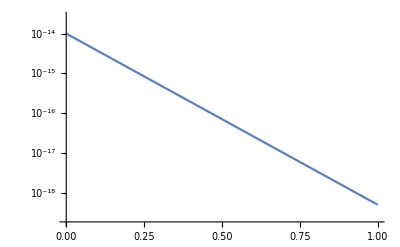

```mathematica
LogPlot[numDen[x],{x,0,1}]
```

Some useful constants
Fermi coupling constant G_F /(hbar c)    1.166 378 7(6)×10^−5 GeV−2

```mathematica
rS = 10^(24);
omega=10^(-19);
rSomega=rS*omega;
gF=1.17*10^(-5);
deltaH[x_] = Sqrt[2]gF numDen[x]/(omega)
thetaV=Pi/6;
```

0.0000165463 10^(5-4.3 x)

Hamiltonian is

```mathematica
hamilM[x_]=rSomega/2{{deltaH[x]-Cos[2thetaV],Sin[2thetaV]},{Sin[2thetaV],-deltaH[x]+Cos[2thetaV]}}
```

{{50000 (-1/2+0.0000165463 10^(5-4.3 x)),25000 √3},{25000 √3,50000 (1/2-0.0000165463 10^(5-4.3 x))}}

The function to be obtained is

```mathematica
nuM[x_]={nuMe[x],nuMx[x]}
```

{nuMe[x],nuMx[x]}

The system becomes

```mathematica
matOsc=I nuM'[x]==hamilM[x].nuM[x]
```

{ⅈ nuMe'[x],ⅈ nuMx'[x]}=={50000 (-1/2+0.0000165463 10^(5-4.3 x)) nuMe[x]+25000 √3 nuMx[x],25000 √3 nuMe[x]+50000 (1/2-0.0000165463 10^(5-4.3 x)) nuMx[x]}

```mathematica
solM=NDSolve[matOsc&&nuM[0]=={1,0},{nuMe,nuMx},{x,0,1}]
```

{{nuMe→InterpolatingFunction[{{0., 1.}}, <>],nuMx→InterpolatingFunction[{{0., 1.}}, <>]}}

```mathematica
probesqrt=nuMe/.solM[[1]]
probxsqrt=nuMx/.solM[[1]]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
Table[probesqrt[i],{i,0,1,0.1}]
probxsqrt[0]
```

{1.+0. ⅈ,0.548862-0.405946 ⅈ,-0.283049-0.287745 ⅈ,-0.0165121+0.237898 ⅈ,0.714223-0.0716439 ⅈ,0.752072+0.00393061 ⅈ,0.366097+0.176751 ⅈ,-0.748286+0.011604 ⅈ,0.532611+0.141354 ⅈ,-0.749329-0.00141921 ⅈ,0.15338-0.196573 ⅈ}

0.+0. ⅈ

```mathematica
norm[x_]=Abs[probesqrt[x]]^2+Abs[probxsqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2

```mathematica
Table[norm[i],{i,0,1,0.1}]
```

{1.,1.00035,1.00067,1.00102,1.00134,1.00166,1.00197,1.00227,1.00257,1.00287,1.00317}

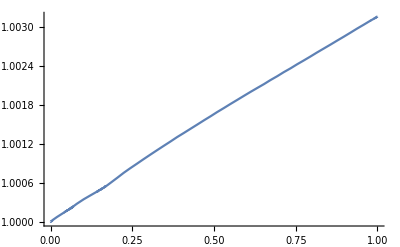

```mathematica
Plot[norm[x],{x,0,1}]
```

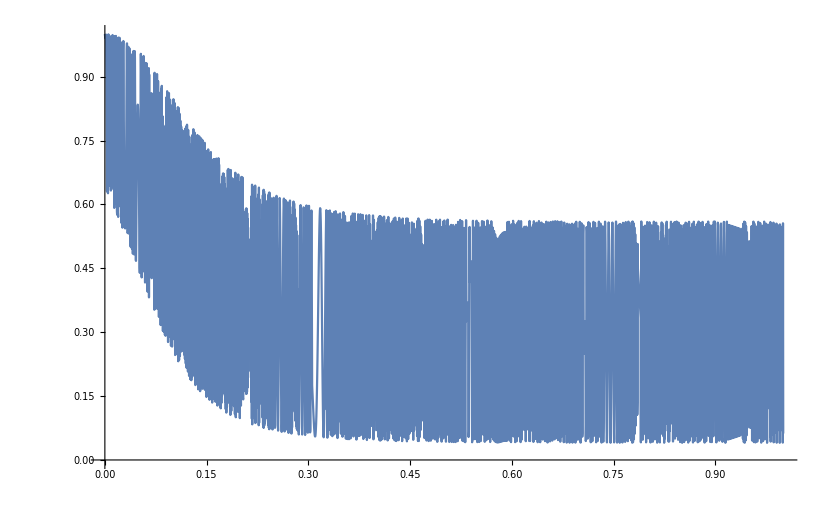

```mathematica
Plot[Abs[probesqrt[x]]^2/norm[x],{x,0,1}]
```

```mathematica
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probxsqrt[x]]^2/norm[x]},{x,0,1},Frame->True,FrameLabel->{"Distance x̂","Probability"},PlotLabel->"Probability of Each Flavor",PlotLegends->Placed[{"ν_e","ν_x"},{Center,Above}],ImageSize->Full]
```

-Graphics-

```mathematica
Abs[probesqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2

```mathematica
biData[end_]:=Table[{Abs[probesqrt[x]]^2,Abs[probxsqrt[x]]^2},{x,0,end,0.01}]
```

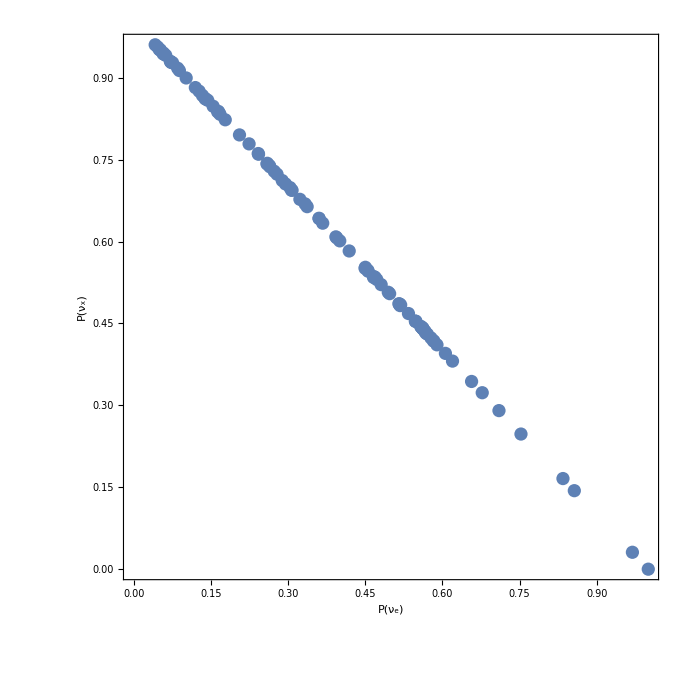

```mathematica
ListPlot[biData[1],FrameLabel->{"P(ν_e)","P(ν_x)"},Frame->True,AspectRatio->1]
```

```mathematica
Manipulate[ListPlot[biData[end],Frame->True,AspectRatio->1,FrameLabel->{"P(ν_e)","P(ν_x)"},PlotRange->{{0,1},{0,1}}],{end,0,1}]
```

```mathematica
triData[end_]:=Table[{Abs[probesqrt[x]]^2,Abs[probxsqrt[x]]^2,x},{x,0,end,0.001}]
```

```mathematica
ListPointPlot3D[triData[1],AxesLabel->{"P(ν_e)","P(ν_x)","x"}]
```

-Graphics3D-

```mathematica
Manipulate[ListPointPlot3D[triData[end],PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1, 1, 2},AxesLabel->{"P(ν_e)","P(ν_x)","x"},ImageSize->Large],{end,0,1}]
```

```mathematica
bi2Data[end_]:=Table[{Sqrt[2]Abs[probesqrt[x]]^2,x},{x,0,end,0.001}]
```

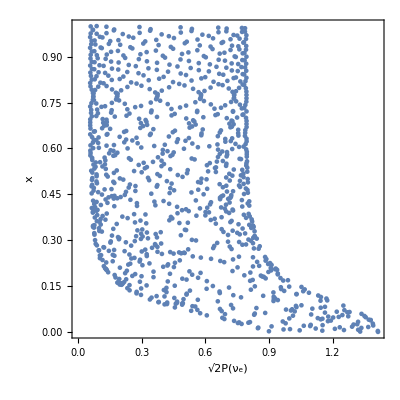

```mathematica
ListPlot[bi2Data[1],Frame->True,AspectRatio->1,FrameLabel->{"√2P(ν_e)","x"}]
```

```mathematica
Manipulate[ListPlot[bi2Data[end],Frame->True,PlotRange->{{0,√2},{0,1}},AspectRatio->1,FrameLabel->{"√2P(ν_e)","x"}],{end,0,1}]
```

### Find out what happened on the path

Assumption: Adiabatic propagation

```mathematica
hamilVDia[x_]=DiagonalMatrix[Eigenvalues[hamilM[x]]]
%//MatrixForm
```

{{-1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x)),0.},{0.,1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x))}}

(-1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x)) | 0.
0. | 1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x)))

```mathematica
Eigensystem[hamilM[x]]
%//MatrixForm
```

{{-1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x)),1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x))},{{-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)+0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))),1.},{-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)-0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))),1.}}}

(-1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x)) | 1. 10^(-4.3 x) √(6.8445×10^9-4.13657×10^9 10^(4.3 x)+2.5×10^9 10^(8.6 x))
{-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)+0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))),1.} | {-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)-0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))),1.})

```mathematica
eigenVectorsM[x_]=Eigenvectors[hamilM[x]]
%//MatrixForm
```

{{-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)+0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))),1.},{-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)-0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))),1.}}

(-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)+0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))) | 1.
-0.57735 10.^(-4.3 x) (-3.30926+1. 10.^(4.3 x)-0.00004 √(6.8445×10^9-4.13657×10^9 10.^(4.3 x)+2.5×10^9 10.^(8.6 x))) | 1.)

```mathematica
eigenVectorsM[0][[1,1]]
```

-0.33335

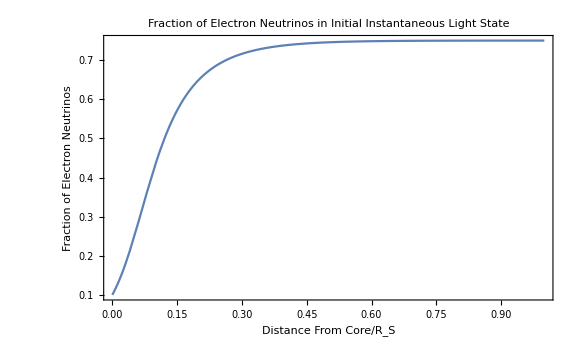

```mathematica
Plot[Abs[eigenVectorsM[x][[1]][[1]]]^2/(Abs[eigenVectorsM[x][[1,1]]]^2+Abs[eigenVectorsM[x][[1,2]]]^2),{x,0,1},PlotRange->Full,Frame->True,ImageSize->Large,PlotLabel->"Fraction of Electron Neutrinos in Initial Instantaneous Light State",FrameLabel->{"Distance From Core/R_S","Fraction of Electron Neutrinos"}]
```

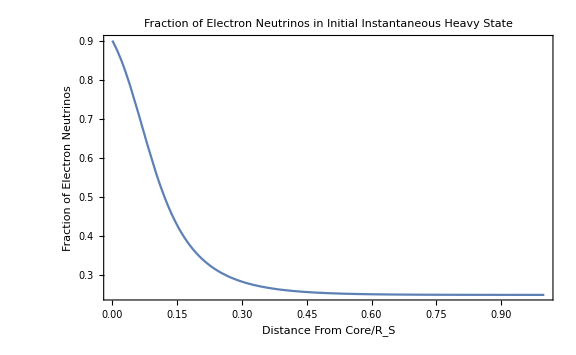

```mathematica
Plot[Abs[eigenVectorsM[x][[2]][[1]]]^2/(Abs[eigenVectorsM[x][[2,1]]]^2+Abs[eigenVectorsM[x][[2,2]]]^2),{x,0,1},PlotRange->Full,Frame->True,ImageSize->Large,PlotLabel->"Fraction of Electron Neutrinos in Initial Instantaneous Heavy State",FrameLabel->{"Distance From Core/R_S","Fraction of Electron Neutrinos"}]
```

```mathematica
Plot[{Abs[eigenVectorsM[x][[1]][[1]]]^2/(Abs[eigenVectorsM[x][[1,1]]]^2+Abs[eigenVectorsM[x][[1,2]]]^2),Abs[eigenVectorsM[x][[2]][[1]]]^2/(Abs[eigenVectorsM[x][[2,1]]]^2+Abs[eigenVectorsM[x][[2,2]]]^2)},{x,0,1},PlotRange->Full,Frame->True,ImageSize->800,PlotLabel->"Fraction of Electron Neutrinos in Instantaneous Light/Heavy State",FrameLabel->{"Distance From Core/R_S","Fraction of Electron Neutrinos"},PlotLegends->Placed[{"Light","Heavy"},{Center,Above}]]
```

-Graphics-